```mathematica
CleanSlate[];
```

contexts purged: {Global`}

approximate kernel memory recovered: 0 Kb

```mathematica
DSolve[{y''[x]+k==0, y[0]==0, y'[l]==0}, y[x], x]
```

{{y[x]→1/2 (2 k l x-k x^2)}}

```mathematica
∫_a^b 1ⅆy
```

-a+b

```mathematica
∫_a^b xⅆx
```

-a^2/2+b^2/2

```mathematica
∫xⅆx
```

x^2/2

```mathematica
DSolve[y'[x]==x, y[x],x]
```

{{y[x]→x^2/2+C[1]}}

```mathematica
sol1=DSolve[{y''[x]==y[x]+x+1, y[0]==0, y'[0]==0}, y[x],x]
```

{{y[x]→-1+ⅇ^x-x}}

```mathematica
sol2=DSolve[{y'[x]==y[x]+x, y[0]==0}, y[x],x]
```

{{y[x]→-1+ⅇ^x-x}}

```mathematica
sol3=DSolve[{y[x]==ⅇ^x-x-1},y[x],x]
```

{{y[x]→-1+ⅇ^x-x}}

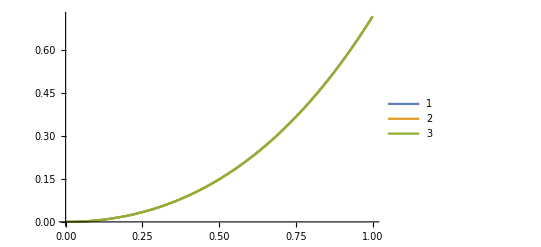

```mathematica
Plot[{y[x]/.sol1,y[x]/.sol2,y[x]/.sol3}, {x, 0,1}, PlotLegends->Automatic]
```

```mathematica
sol4=DSolve[{y''[x]+1/x y'[x]-1/x^2 y[x]==6/x^2, y[1]==1, y[1.5]==-1}, y[x],x]
```

{{y[x]→(0.4 (16.5-15. x+1. x^2))/x}}

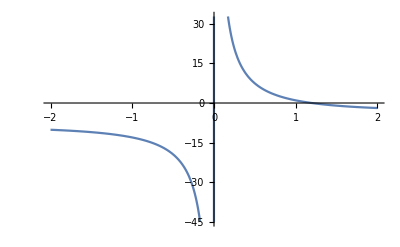

```mathematica
Plot[y[x]/.sol4,{x,-2,2}]
```

```mathematica
sol5=DSolve[{y'[x]==(x+y[x])/x, y[2]==2}, y[x],x]
```

{{y[x]→x-x Log[2]+x Log[x]}}

```mathematica
y[x]/.sol5/.x->2.5
```

{3.05786}

```mathematica
y[x]/.sol5/.x->3.0
```

{4.2164}